```mathematica
Par := f |-> (f[2] == f[-2])
Impar := f |-> (f[-2] == -f[2])
Tipo := f |-> Which[Par[f], "Par", Impar[f], "Impar", !Par[f] || !Impar[f], "Nope"]
```

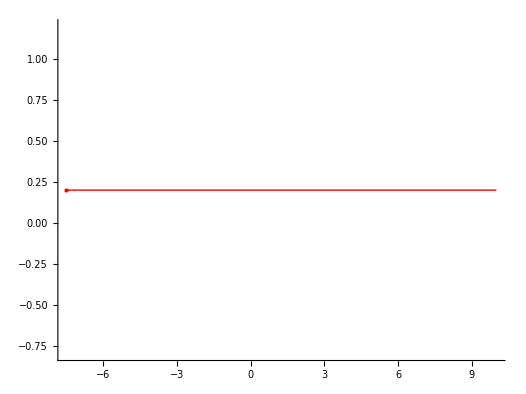

```mathematica
Graphics[{Thick,Red,Line[{{-15/2,0.2},{10,0.2}}],{PointSize[Large],Point[{-15/2,0.2}]},White,PointSize[Medium],(*Point[{-4,0.2}]*)},Axes->{True,False},PlotRange->{{-10,10},{0,0}}]
```

```mathematica
Simplify[(√(10-3x)+√(2x+15))/(x^2-9)]
```

(√(10-3 x)+√(15+2 x))/(-9+x^2)

```mathematica
(2+ 7ⅈ )+(4+2ⅈ)
```

6+9 ⅈ

```mathematica
(2+ 7ⅈ )*(4+ 2ⅈ)
```

-6+32 ⅈ

```mathematica
(3-8ⅈ) *(8+ 2ⅈ)
```

40-58 ⅈ

```mathematica
(3-8ⅈ) + (8+ 2ⅈ)
```

11-6 ⅈ

```mathematica
Solve[x^2+2x+1==-2+1, x]
```

{{x→-1-ⅈ},{x→-1+ⅈ}}

```mathematica
10^2+4/5 x+(4/(2 5))^2==(10+4/(2 5))^2
```

2504/25+(4 x)/5==2704/25

```mathematica
√23 √3==√(23 3)
```

True

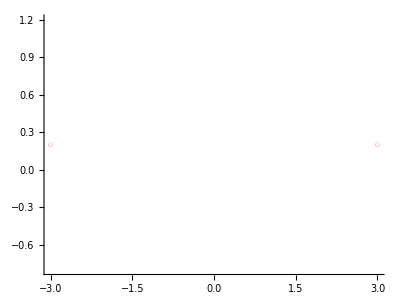

```mathematica
Graphics[{Thick,Red,(*Line[{{10/3,0.2},{-10,0.2}}]*) ,{PointSize[Large],Point[{3,0.2}]}, {PointSize[Large],Point[{-3,0.2}]},White,PointSize[Medium],Point[{-3,0.2}], Point[{3,0.2}]},Axes->{True,False},PlotRange->{{-10,10},{0,0}}]
```

```mathematica
(-8+5ⅈ)(1-3ⅈ) == (-8+5ⅈ)Re[(1-3ⅈ)] +(-8+5ⅈ) Im[(1-3ⅈ)]ⅈ
```

True

```mathematica
Simplify[(1/((√(x+3))^2-5))]
```

1/(-2+x)

```mathematica
Plo
```

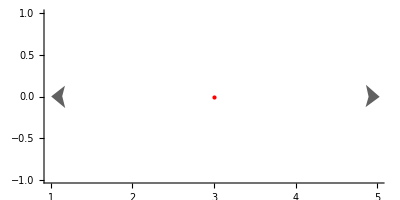

```mathematica
Graphics[{Thick,Red,(*Line[{{10/3,0.2},{-10,0.2}}]*) ,{PointSize[Large],Point[{3,0}]},(*White,PointSize[Medium],Point[{-3,0.2}], Point[{3,0.2}]*)},Axes->{True,False},PlotRange->{{1,5},{0,0}}]
```

```mathematica
Prime[100000]
```

1299709

```mathematica
3^2-8(3)+16
```

1

```mathematica
-10/3 3+11
```

1

```mathematica
Tipo[x|->(x+1)^2]
```

Nope

```mathematica
Tipo[x|->-x-5^2]
```

Nope

```mathematica
Tipo[x|->x^2]
```

Par